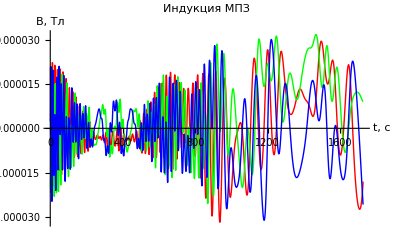

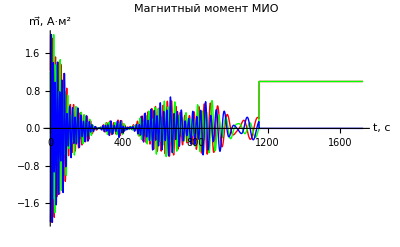

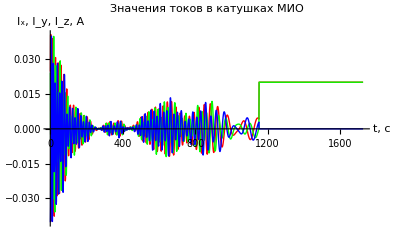

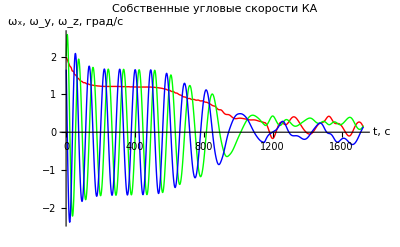

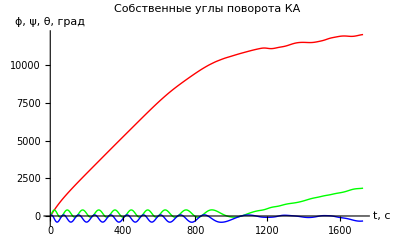

ListLinePlot::prng: Value of option PlotRange -> {Min[-0.0000142879, 0.102244\ (-0.0000171272 - 0.02\ (0.0346575  - ωx0) + 0.03\ (0.0350153  - ωy0)), 0.102244\ (-0.00015967 + 0.02\ (0.0346575  - ωx0) - 0.03\ (0.0288717  - ωz0)), 0.102244\ (0.000174778  - 0.02\ (0.0350153  - ωy0) + 0.02\ (0.0288717  - ωz0))], Max[0.0000925039, « 2 », « 20 »\ (« 1 »)]}
 is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

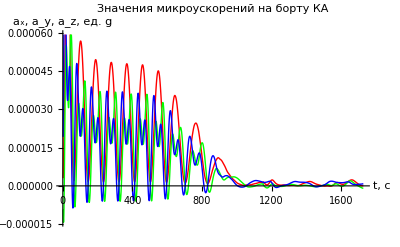

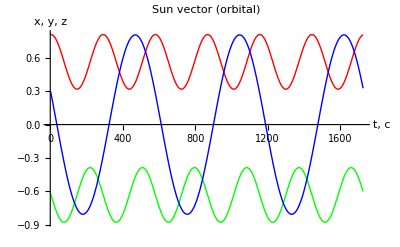

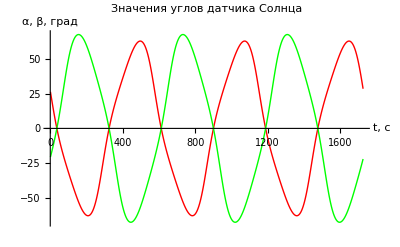

```mathematica
Off[General::spell1]
Off[General::spell]
<<PlotLegends`;
μ0 = 1.257*10^-6;

(*Earth's constants*)
RE = 6377000;
ME = 5.977*10^24;
μE = 3.986*10^14;
ωE = (2*π)/(24*60*60);
LE = 8.1*10^22;
gE = 9.78049;
ϵE = 0.3839724354387525;
ωYear=(2*π)/(24*60*60*365);

(*Orbit paramaters*)
λΩ0 = 60.3 * Degree;
t = 62.8*Degree;
ω = 50.5 * Degree;
a = RE + 570*10^3;
ϵ = 0.00126;
T = 2*π*√(a^3/μE);
Sg = 20*Degree;

(*Sapacecraft parameters*)
m = 50;
lx = 0.6;
ly = 0.4;
lz = 0.4;
rDx = lx/2;
rDy = 0;
rDz = 0;
Jx = 1/(2*π)*m*ly*lz;
Jy = 1/(2*π)*m*lx*lz;
Jz = 1/(2*π)*m*lx*ly;
bx = 0.5*lx;
by = 0.5*ly;
bz = 0.5*lz;

(*Coil parameters*)
l = 0.2;
D1 = 5.1*10^-3;
D2 = 10*10^-3;
d = 0.33*10^-3;
k3 = 0.44;

(*Atmosphere params*)
a1 = -16.559;
a2 = 0.6982;
a3 = 75.401;

b1 = -0.3839;
b2 = 0.2902*0.01;
b3 = 0.2051*10^-5;

c1 = -0.247;
c2 = 0.00199;
c3 = 3.495;
c4 = -707.58;
c5 = 278.35;

d1 = -0.7379;
d2 = 0.008524;
d3 = -0.5328*10^-5;

e1 = -0.182;
e2 = 0.001826;
e3 = -0.1289*10^-5;
e4 = 1;
e5 = 4;

F0 = 150;
F = 150;
ap = 12;
fi = 90 * Degree;
Ad = 0.09;
k = 4.7;
Cx = 2;

(*Earth magnetic field model params*)
CurrentYear = 2010;
IMag1965 = ({{-30339, -2123, 0, 0, 0, 0, 0, 0, 0}, {-1654, 2994, 1567, 0, 0, 0, 0, 0, 0}, {1297, -2036, 1298, 843, 0, 0, 0, 0, 0}, {958, 805, 492, -392, 256, 0, 0, 0, 0}, {-223, 357, 246, -26, -161, -51, 0, 0, 0}, {47, 60, 4, -229, 3, -4, -122, 0, 0}, {71, -54, 0, 12, -25, -9, 13, -2, 0}, {10, 9, -3, -12, -4, 7, -5, 12, 6}});
JMag1965 = ({{0, 5758, 0, 0, 0, 0, 0, 0, 0}, {0, -2006, 120, 0, 0, 0, 0, 0, 0}, {0, -403, 242, -176, 0, 0, 0, 0, 0}, {0, 149, -280, 8, -256, 0, 0, 0, 0}, {0, 16, 125, -123, -107, 77, 0, 0, 0}, {0, -14, 106, 68, -32, -10, -13, 0, 0}, {0, -57, -27, -8, 9, 23, -19, -17, 0}, {0, 3, -13, 5, -17, 4, 22, -3, -16}});
dIMag = ({{15.3, 8.7, 0, 0, 0, 0, 0, 0, 0}, {-24.4, 0.3, -1.6, 0, 0, 0, 0, 0, 0}, {0.2, -10.8, 0.7, -3.8, 0, 0, 0, 0, 0}, {-0.7, 0.2, -3.0, -0.1, -2.1, 0, 0, 0, 0}, {1.9, 1.1, 2.9, 0.6, 0, 1.3, 0, 0, 0}, {-0.1, -0.3, 1.1, 1.9, -0.4, -0.4, -0.2, 0, 0}, {-0.5, -0.3, 0.7, -0.5, 0.3, 0, -0.2, -0.6, 0}, {0.1, 0.4, 0.6, 0, 0, -0.1, 0.3, -0.3, -0.5}});
dJMag = ({{0, -2.3, 0, 0, 0, 0, 0, 0, 0}, {0, -11.8, -16.7, 0, 0, 0, 0, 0, 0}, {0, 4.2, 0.7, -7.7, 0, 0, 0, 0, 0}, {0, -0.1, 1.6, 2.9, -4.2, 0, 0, 0, 0}, {0, 2.3, 1.7, -2.4, 0.8, -0.3, 0, 0, 0}, {0, -0.9, -0.4, 2.0, -1.1, -0.1, -0.9, 0, 0}, {0, -1.1, 0.3, 0.4, 0.2, 0.4, 0.2, 0.3, 0}, {0, 0.1, -0.2, -0.3, -0.2, -0.3, -0.4, -0.3, -0.3}});
IMag = IMag1965 + dIMag*(CurrentYear - 1965);
JMag = JMag1965 + dJMag*(CurrentYear - 1965);

(*Modelling*)

Ng = 1;
tFin = 3*T;
dt = 10;
NCount = Floor[tFin/dt];
SwG = 1;
SwA = 1;
SwC = 1;
α = 10^6;
LMax = 2;
ϕ = 15*Degree;
ψ = 55*Degree;
ν = 75*Degree;
ωx = 2*Degree;
ωy = 1.8*Degree;
ωz = 1.9*Degree;
ϕD = 0;
ψD = 0;
θD = 0;
BxEx = 0;
ByEx = 0;
BzEx = 0;
ωxEx = ωx0;
ωyEx = ωy0;
ωzEx = ωz0;
λ0 =N[ Cos[ϕ/2]*Cos[ψ/2]*Sin[ν/2] + Sin[ϕ/2]*Sin[ψ/2]*Sin[ν/2]];
λ1 = N[Cos[ϕ/2]*Cos[ψ/2]*Cos[ν/2] - Sin[ϕ/2]*Sin[ψ/2]*Cos[ν/2]];
λ2 = N[Sin[ψ/2]*Cos[ϕ/2]*Cos[ν/2] + Sin[ϕ/2]*Cos[ψ/2]*Sin[ν/2]];
λ3 = N[Sin[ϕ/2]*Cos[ψ/2]*Cos[ν/2] - Sin[ϕ/2]*Cos[ψ/2]*Sin[ν/2]];

θEuler = ν;
ψEuler = ψ;
ϕEuler = ϕ;

(*Outdata ivars*)
BxTable = Range[NCount-1];
ByTable = Range[NCount-1];
BzTable = Range[NCount-1];

LTable={Range[NCount-1],Range[NCount-1],Range[NCount-1]};
SunVecTableOrbit={Range[NCount-1],Range[NCount-1],Range[NCount-1]};
SunVecTableInert={Range[NCount-1],Range[NCount-1],Range[NCount-1]};
IxTable = Range[NCount - 1];
IyTable = Range[NCount - 1];
IzTable = Range[NCount - 1];

aixTable = Range[NCount-1];
aiyTable = Range[NCount-1];
aizTable = Range[NCount-1];

ωxTable = Range[NCount-1];
ωyTable = Range[NCount-1];
ωzTable = Range[NCount-1];

axTable = Range[NCount];
ayTable = Range[NCount];
azTable = Range[NCount];
alphaList=ConstantArray[0,NCount -1];
betaList=ConstantArray[0,NCount - 1];

axTable[[1]] = 0;
ayTable[[1]] = 0;
azTable[[1]] = 0;
sunOrientation  = False;
sunTreshold = 0.04;
uniTable  = Range[NCount*1];
LKin = 0;
αRotation = 0;

dmGrav=0.2;
lGrav=2;

deltaU=tempDeltaU=0.01093;
u =0;
αk2=Abs[(Bx*By)/Jx];
βk2=Abs[(Bx*By)/Jy];
αh=√αk2*1;
βh=√βk2*1;
aip1[ai_,aim1_, βVal_]=(((By)^2*(dt)^2)/Jx*βVal-((dt)^2*αk2-2)*ai-(1-(dt*αh)/Jx)*aim1)/(1+(dt*αh)/Jx);
bip1[bi_,bim1_, αVal_]=(((Bx)^2*(dt)^2)/Jy*αVal-((dt)^2*βk2-2)*bi-(1-(dt*βh)/Jy)*bim1)/(1+(dt*βh)/Jy);

ωtxm = 0;
ωtym = 0;
ωtzm = 0;
(*Main cycle*)
For[n=1,n<NCount,n++,

f = ({{λ0^2+λ1^2-λ2^2-λ3^2, 2*(λ1*λ2+λ0*λ3), 2*(λ1*λ3-λ0*λ2)}, {2*(λ1*λ2-λ0*λ3), λ0^2-λ1^2+λ2^2-λ3^2, 2*(λ2*λ3+λ0*λ1)}, {2*(λ1*λ3+λ0*λ2), 2*(λ2*λ3-λ0*λ1), λ0^2-λ1^2-λ2^2+λ3^2}});

τ = Floor[(n*dt)/T]*T;
cycleNo=Floor[(n*dt)/T];
EResult =FindRoot[Ee-ϵ*Sin[Ee] - (2*π)/T*(n*dt - τ)==0, {Ee, 0}];
r=a*(1-ϵ*Cos[Ee])/.EResult;


SinV = N[Sin[Ee]/(1-ϵ*Cos[Ee])*√(1-ϵ^2)]/.EResult;
CosV =N[ (Cos[Ee]-ϵ)/(1-ϵ*Cos[Ee])]/.EResult;

prevU = u;
u=N[Which[(SinV≥0)&&(CosV≥0), ω + ArcSin[SinV],
(CosV<0), ω + π - ArcSin[SinV],
(SinV<0)&&(CosV≥0), ω + 2*π + ArcSin[SinV]]];
deltaU = u - prevU;
deltaU =If[ deltaU>1||deltaU<-1,0.01093,deltaU];

(*Sun vectors*)
SInert =({{Cos[u]}, {Sin[u]}, {Sin[u]*Cos[t]}}) ;

InertToOrbital=({{Cos[u]*Cos[λΩ0]-Cos[t]*Sin[u]*Sin[λΩ0], Cos[u]*Sin[λΩ0]+Cos[t]*Sin[u]*Cos[λΩ0], Sin[t]*Sin[u]}, {-Sin[u]*Cos[λΩ0]-Cos[t]*Cos[u]*Sin[λΩ0], -Sin[u]*Sin[λΩ0]+Cos[t]*Cos[u]*Cos[λΩ0], Sin[t]*Cos[u]}, {Sin[t]*Sin[λΩ0], -Sin[t]*Cos[λΩ0], Cos[t]}});
SOrbital=InertToOrbital.SInert;
SunVecTableOrbit⟦1⟧⟦n⟧=SOrbital⟦1⟧⟦1⟧;
SunVecTableOrbit⟦2⟧⟦n⟧=SOrbital⟦2⟧⟦1⟧;
SunVecTableOrbit⟦3⟧⟦n⟧=SOrbital⟦3⟧⟦1⟧;
alphaList⟦n⟧=ArcTan[-(SOrbital⟦3⟧⟦1⟧)/(SOrbital⟦2⟧⟦1⟧)];
betaList⟦n⟧=ArcTan[-(SOrbital⟦3⟧⟦1⟧)/(SOrbital⟦1⟧⟦1⟧)];

CosO = Evaluate[Sin[t]*Sin[u]];
θ = Evaluate[ArcCos[CosO]];
tgl = Cos[t]*Tan[u];
cosl =Cos[u]*Sin[θ];
lPrefix = λΩ0-0.0016*(RE/a)*Cos[t]/((1-ϵ^2)^2)*(2*π*n*dt)/T-ωE*n*dt-Sg;
λ = N[Which[(tgl ≥ 0) && (cosl ≥0), lPrefix + ArcTan[tgl],
(cosl <0),lPrefix + π + ArcTan[tgl],
(tgl < 0) && (cosl ≥0),lPrefix + 2*π + ArcTan[tgl]]];


Bxg =10^-9*∑_(ni=1)^Ng ∑_(mi=0)^ni ((IMag⟦ni, mi+1⟧*Cos[mi*λ]+JMag⟦ni, mi+1⟧*Sin[mi*λ])*(RE/r)^(ni+2)*(-√((If[mi==0,1,2]*(ni-mi)!)/((ni+mi)!)))*(Sin[θ]^mi*∑_(si=0)^Floor[(ni-mi)/2] ((ni-mi-2*si)*(-1)^si*(2*ni-2*si)!/(2^ni*si!*(ni-si)!*(ni-2*si-mi)!)*Cos[θ]^(ni-mi-2*si-1)*Sin[θ])+ mi*Sin[θ]^(mi-1)*Cos[θ]*∑_(si=0)^Floor[(ni-mi)/2] ((-1)^si*(2*ni - 2*si)!/(2^ni*si!*(ni-si)!*(ni-2*si-mi)!)*Cos[θ]^(ni-mi-2*si)))); 
Byg = 10^-9*∑_(ni=1)^Ng ∑_(mi=0)^ni ((IMag⟦ni, mi+1⟧*Sin[mi*λ]-JMag⟦ni, mi+1⟧*Cos[mi*λ])*(RE/r)^(ni+2)*(mi/Sin[θ] √((If[mi==0,1,2]*(ni-mi)!)/((ni+mi)!)))*Sin[θ]^mi*∑_(si=0)^Floor[(ni-mi)/2] ((-1)^si*(2*ni-2*si)!/(2^ni*si!*(ni-si)!*(ni-2*si-mi)!)*Cos[θ]^(ni-mi-2*si)));

Bzg = 10^-9*∑_(ni=1)^Ng ∑_(mi=0)^ni ((IMag⟦ni, mi+1⟧*Cos[mi*λ]+JMag⟦ni, mi+1⟧*Sin[mi*λ])*(RE/r)^(ni+2)*((ni+1)√((If[mi==0,1,2]*(ni-mi)!)/((ni+mi)!)))*Sin[θ]^mi*∑_(si=0)^Floor[(ni-mi)/2] ((-1)^si*(2*ni-2*si)!/(2^ni*si!*(ni-si)!*(ni-2*si-mi)!)*Cos[θ]^(ni-mi-2*si)));

SinK = Cos[t]/Sin[θ];
CosK = cosl*Sin[t];
Bx0 = Bxg *CosK+Byg*SinK;
By0 = Bxg *SinK-Byg*CosK;
Bz0 = Bzg;

({{Bx}, {By}, {Bz}}) = f.({{Bx0}, {By0}, {Bz0}});

BxTable[[n]] = Bx;
ByTable[[n]] = By;
BzTable[[n]] = Bz;

h = (r-RE)/1000;
atm = Which[h>600, 0, h≤600,1];
k1 = 1+(c1+h*c2+c3*ⅇ^((-(h+c4)^2)/c5^2))*Cos[fi/2]^k;
k2 = 1+(d1+d2*h+d3*h^2)*Ad;
k3 = 1+ (b1+b2*h+b3+h^2)*(F-F0)/F0;
k4 = 1+ (e1+e2*h+e3*h^2)*Log[ap/e5+e4];


ρ = k1*k2*k3*k4*ⅇ^(a1-a2*√(h-a3));
V1 = √((μE+(1-ϵ^2))/a)*1/(1-ϵ*Cos[Ee])-ωE*r*Cos[t]/.EResult;
V2 = ωE*r*Cos[t]*Cos[u];
V3 = √(μE/a)*(ϵ*Sin[Ee])/(1-ϵ*Cos[Ee])/.EResult;
(*V = ({{V1}, {V2}, {V3}});*)
V = {V1, V2, V3};

({{lx0}, {ly0}, {lz0}}) = Inverse[f].({{lx}, {ly}, {lz}});
S = ly0*lz0;


BxEx = Bx;
ByEx = By;
BzEx = Bz;

aVecLength=Sqrt[ωx^2+ωy^2+ωz^2];
gain=N[If[aVecLength>0.04,α,α/1.41]];

Lnx  = 9;
Lny  = 0;
Lnz  = 0;

If[cycleNo <2,
(*Stabilization*)
Lnx  = gain*(Jy*ωy*Bz - Jz*ωz*By);
Lny  = gain*(Jz*ωz*Bx - Jx*ωx*Bz);
Lnz  = gain*(Jx*ωx*By - Jy*ωy*Bx);
,
(*Sun orientation*)
Lnx  =1;
Lny  =1;
Lnz  = α*Bx*By*Sin[alphaList⟦n⟧];
];

Lx = Evaluate[Which[Lnx<-LMax, -LMax, Lnx>LMax, LMax, True, Lnx]];
Ly = Evaluate[Which[Lny<-LMax, -LMax, Lny>LMax, LMax, True, Lny]];
Lz = Evaluate[Which[Lnz<-LMax, -LMax, Lnz>LMax, LMax, True, Lnz]];

LTable[[1]][[n]] = Lx;
LTable[[2]][[n]] = Ly;
LTable[[3]][[n]] = Lz;

IPostfix = d^2/(2*k3*(D2-D1))*((1.266*40)/(0.25*1.25*10^6*D1^2*l-0.403*Lx)+4.72/(D1^0.3*l^2.7));

Ix = Lx*IPostfix;
Iy = Ly*IPostfix;
Iz = Lz*IPostfix;

IxTable[[n]] = Ix;
IyTable[[n]] = Iy;
IzTable[[n]] = Iz;

NormV = Norm[V];

Mx = SwG*3*μE/r^3*f⟦2,3⟧*f⟦3,3⟧*(Jz - Jy)+SwA*atm*ρ*NormV*S*Cx/2*(rDz*(V1*f⟦1,2⟧+V2*f⟦2,2⟧+V3*f⟦3,2⟧) - rDy*(V1*f⟦1,3⟧+V2*f⟦2,3⟧+V3*f⟦3,3⟧))+SwC*(Ly*Bz - Lz*By);

My = SwG*3*μE/r^3*f⟦3,3⟧*f⟦1,3⟧*(Jx - Jz)+SwA*atm*ρ*NormV*S*Cx/2*(rDx*(V1*f⟦1,3⟧+V2*f⟦2,3⟧+V3*f⟦3,3⟧) - rDz*(V1*f⟦1,1⟧+V2*f⟦2,1⟧+V3*f⟦3,1⟧))+SwC*(Lz*Bx - Lx*Bz);

Mz = SwG*3*μE/r^3*f⟦2,3⟧*f⟦1,3⟧*(Jy - Jx)+SwA*atm*ρ*NormV*S*Cx/2*(rDx*(V1*f⟦1,1⟧+V2*f⟦2,1⟧+V3*f⟦3,1⟧) - rDz*(V1*f⟦1,2⟧+V2*f⟦2,2⟧+V3*f⟦3,2⟧))+SwC*(Lx*By - Ly*Bx);

ωx = ωx+((Jy-Jz)/Jx*ωy*ωz+Mx/Jx)*dt;
ωy = ωy+((Jz-Jx)/Jy*ωx*ωz+My/Jy)*dt;
ωz = ωz+((Jx-Jy)/Jz*ωx*ωy+Mz/Jz)*dt;

ωxTable[[n]] = ωx/Degree;
ωyTable[[n]] = ωy/Degree;
ωzTable[[n]] = ωz/Degree;

({{rx}, {ry}, {rz}}) = f.({{0}, {0}, {r}}); 
ax = μE/r^3*((3*(bx*rx+by*ry+bz*rz))/r^2*rx - bx)+(Cx*S)/(2*m)*ρ*NormV*V1-(ωx*(ωy*by + ωz*bz) - (ωy^2 + ωz^2)*bx + (ωy-ωyEx)/dt*bz - (ωz - ωzEx)/dt*by);

ay = μE/r^3*((3*(bx*rx+by*ry+bz*rz))/r^2*ry - by)+(Cx*S)/(2*m)*ρ*NormV*V2-(ωy*(ωz*bz + ωx*bx) - (ωx^2 + ωz^2)*by + (ωz-ωzEx)/dt*bx - (ωx - ωxEx)/dt*bz);

az = μE/r^3*((3*(bx*rx+by*ry+bz*rz))/r^2*rz - bz)+(Cx*S)/(2*m)*ρ*NormV*V3-(ωz*(ωx*bx + ωy*by) - (ωx^2 + ωy^2)*bz + (ωx-ωxEx)/dt*by - (ωy - ωyEx)/dt*bx);

aixTable[[n]] =ax/ gE;
aiyTable[[n]] =ay/ gE;
aizTable[[n]] =az/ gE;

{newXAngle, newYAngle, newZAngle} ={ωx*dt/Degree, ωy*dt/Degree, ωz*dt/Degree}; 

newXAngle = axTable[[n]]+newXAngle;
newYAngle = ayTable[[n]]+newYAngle;
newZAngle = azTable[[n]]+newZAngle;

axTable[[n+1]] =newXAngle;(*Which[newXAngle>180,newXAngle-360,newXAngle<-180,newXAngle+360, True, newXAngle];*)
ayTable[[n+1]] =newYAngle;(*Which[newYAngle>180,newYAngle-360,newYAngle<-180,newYAngle+360, True, newYAngle];*)
azTable[[n+1]] =newZAngle;(*Which[newZAngle>180,newZAngle-360,newZAngle<-180,newZAngle+360, True, newZAngle];*)

ωxEx = ωx;
ωyEx = ωy;
ωzEx = ωz;

λ0 = λ0 - 1/2*(ωx*λ1 + ωy*λ2 + ωz*λ3)*dt;
λ1 = λ1 + 1/2*(ωx*λ0 + ωz*λ2 - ωy*λ3)*dt;
λ2 = λ2 + 1/2*(ωy*λ0 + ωx*λ3 - ωz*λ1)*dt;
λ3 = λ3 + 1/2*(ωz*λ0 + ωy*λ1 - ωx*λ2)*dt;

];


ListLinePlot[{BxTable, ByTable, BzTable}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]},
PlotRange->{Min[BxTable,ByTable,BzTable],
		    Max[BxTable,ByTable,BzTable]},
AxesStyle->Directive[16],
AxesLabel->{"t, с","B, Тл"}, 
PlotLegend->{"B_X", "B_Y", "B_Z"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Индукция МПЗ"]

ListLinePlot[LTable, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[LTable],Max[LTable]},
AxesStyle->Directive[16],
AxesLabel->{"t, с","m⃗, A·(:043c)^2"}, 
PlotLegend->{"m_X", "m_Y", "m_Z"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Магнитный момент МИО"]

ListLinePlot[{IxTable, IyTable, IzTable}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[IxTable, IyTable, IzTable], Max[IxTable, IyTable, IzTable]},
AxesStyle->Directive[16], 
AxesLabel->{"t, с","I_x, I_y, I_z, A"},
PlotLegend->{"I_x", "I_y", "I_z"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Значения токов в катушках МИО"]

ListLinePlot[{ωxTable, ωyTable, ωzTable}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[ωxTable,ωyTable,ωzTable],Max[ωxTable,ωyTable,ωzTable]},  
AxesStyle->Directive[16], 
AxesLabel->{"t, с","ω_x, ω_y, ω_z, град/с"},
PlotLegend->{"ω_x", "ω_y", "ω_z"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Собственные угловые скорости КА"]

ListLinePlot[{axTable, ayTable, azTable}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[axTable, ayTable, azTable], Max[axTable, ayTable, azTable]},
AxesStyle->Directive[16], 
AxesLabel->{"t, с","ϕ, ψ, θ, град"},
PlotLegend->{"ϕ", "ψ", "θ"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Собственные углы поворота КА"]

ListLinePlot[{aixTable, aiyTable, aizTable}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[aixTable, aiyTable, aizTable], Max[aixTable, aiyTable, aizTable]},
AxesStyle->Directive[16], 
AxesLabel->{"t, с","a_x, a_y, a_z, ед. g"},
PlotLegend->{"a_x", "a_y", "a_z"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Значения микроускорений на борту КА"]


ListLinePlot[SunVecTableOrbit, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0], RGBColor[0,0,1]}, 
PlotRange->{Min[SunVecTableOrbit], Max[SunVecTableOrbit]},
AxesStyle->Directive[16], 
AxesLabel->{"t, с","x, y, z"},
ImageSize->Scaled[0.8],
PlotLabel->"Sun vector (orbital)"]

ListLinePlot[{alphaList/Degree, betaList/Degree}, 
PlotJoined->True, 
PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0]}, 
PlotRange->Automatic,
AxesStyle->Directive[16], 
AxesLabel->{"t, с","α, β, град"},
PlotLegend->{"α", "β"},
LegendPosition->{1.1,-0.4},
ImageSize->Scaled[0.8],
PlotLabel->"Значения углов датчика Солнца"]


Clear["Global`*"];
```